### What we have

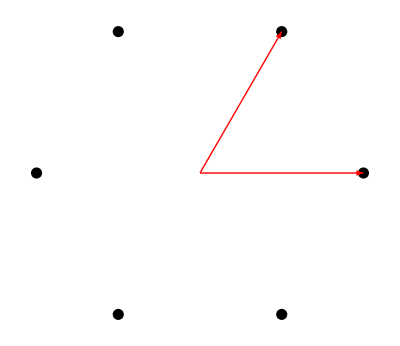

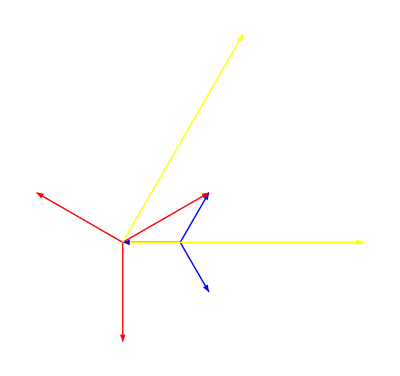

```mathematica
delta = {{1/2,√3/2},{-1,0},{1/2,-√3/2}};
a = {delta[[2]]-delta[[3]], delta[[3]]-delta[[1]], delta[[1]]-delta[[2]]};
b = {{(4*π)/3,0}, {(2*π)/3,(2*π)/(√3)}};
Graphics[{
{Black,PointSize[0.02], Point[#]} & /@ CirclePoints[{(4*π)/3,0},6],
{Red, Arrow[{{0,0},{0,0}+#}]}&/@b
}]
Graphics[{
{Blue, Arrow[{-delta[[2]],-delta[[2]]+#}]}&/@delta,
{Red, Arrow[{{0,0},{0,0}+#}]}&/@a,
{Yellow, Arrow[{{0,0},{0,0}+#}]} & /@ b
}]
```

### What we want

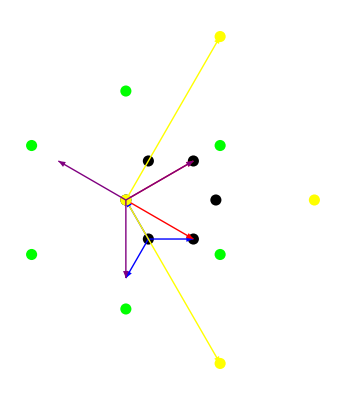

{{1,0},{-1/2,(√3)/2},{-1/2,-(√3)/2}}

{{3/2,(√3)/2},{0,-√3},{-3/2,(√3)/2}}

{{(2 π)/3,(2 π)/(√3)},{(2 π)/3,-(2 π)/(√3)}}

```mathematica
alength = 1;
latticepoints =  {alength,0}+ # & /@ CirclePoints[{alength,0},6];
delta = alength/2*{{2,0}, {-1, √3},-{1, √3}};
a = alength*{ {3/2, √3/2},{3/2, -√3/2}};
c=(2*π)/(3*alength)*{{1, √3},{ 1, -√3}};
K = (2*π)/(3*alength){{1, 1/(√3)},{1,-1/(√3)}};
NNNChiral = {a[[1]], a[[2]]-a[[1]], -a[[2]]};
reciprocallattice = {K[[1]], K[[2]], K[[1]]-K[[2]], -K[[1]], -K[[2]], K[[2]]-K[[1]]};
BZpoints = {c[[1]], c[[2]], c[[1]]+c[[2]], {0,0}};
Graphics[{
{Black,PointSize[0.02], Point[#]} & /@ latticepoints,
{Blue, Arrow[{-delta[[2]],-delta[[2]]+#}]}&/@delta,
{Red, Arrow[{{0,0},{0,0}+#}]}&/@a,
{Yellow, Arrow[{{0,0},{0,0}+#}]} & /@ c,
{Yellow, PointSize[0.02], Point[#]} &/@ BZpoints,
{Green,PointSize[0.02], Point[#]} & /@ reciprocallattice,
{Purple, Arrow[{{0,0},{0,0}+#}]}& /@ NNNChiral
}]
delta
NNNChiral
c
```